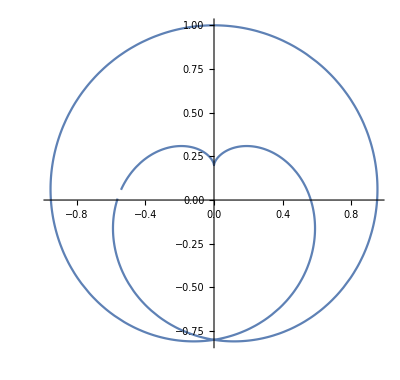

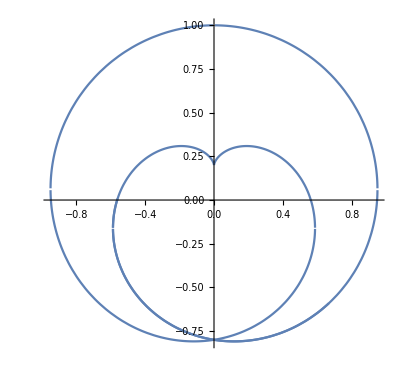

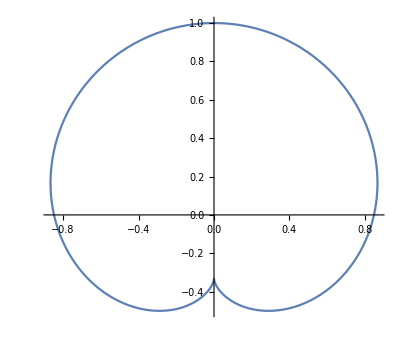

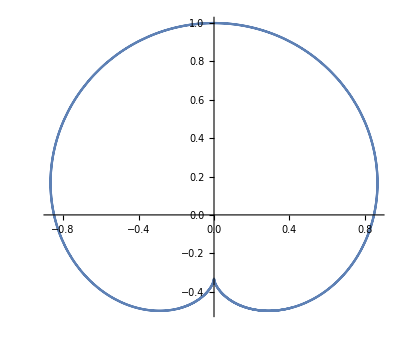

```mathematica
ClearAll["Global`*"]

F[x_,y_,t_,f_,g_]:=Sin[2*Pi*(g[f[t]]-g[t])]-y*(Sin[2*Pi*g[f[t]]]-Sin[2*Pi*g[t]])-x*(Cos[2*Pi*g[f[t]]]-Cos[2*Pi*g[t]]);

Fd[x_,y_,t_,f_,g_]:= 2 Pi( f'[t] g'[f[t]](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[f[t]]]+x Sin[2 Pi g[f[t]]])-g'[t](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[t]] +x Sin[2 Pi g[t]]) );

parametricFunc[t_,f_,g_]:={x,y}/.(Solve[F[x,y,t,f,g]==0&&Fd[x,y,t,f,g]==0,{x,y}]);

plot[f_,g_,from_,to_]:=ParametricPlot[parametricFunc[t,f,g],{t,from,to}];
(* Heart *)
f[x_]:=x*3;
g1[x_]:=x/2^Floor[Log[x]];
plot[f, g1, E,E^2-0.698]

f[x_]:=x*1.5;
g2[x_]:=x/2;
plot[f, g2, E,E^2]
(* Original Cardioid *)
f[x_]:=x*4;
g1[x_]:=x/2^Floor[Log[x]];
plot[f, g1, E,E+2]

f[x_]:=x*2;
g2[x_]:=x/2;
plot[f, g2, E,E^2]
```